```mathematica
(* Adaptive Gaussian *)

adapTabuIner = { {20,670.96 }, {30,866.17 }, {35, 1049.49}, {40,1167.07 }, {45, 1414.45}, {50, 1531.04}, {100, 3295.11}, {250, 7994.09} };

adapTabuSil = { {20,0.25 }, {30,-0.09 }, {35, -0.08}, {40,0.27}, {45, -0.02}, {50,0.13 }, {100,0.05 }, {250, 0.02} };

adapTabuHom= { {20, 0.29}, {30,0.21 }, {35, 0.03}, {40,0.14}, {45, 0.20}, {50, 0.14}, {100, 0.09}, {250, 0.10} };

adapTabuCom = { {20, 0.31}, {30, 0.24}, {35, 0.03}, {40, 0.23}, {45,0.31 }, {50,0.16 }, {100,0.20 }, {250, 0.11} };

adapTabuVm= { {20, 0.30}, {30, 0.22}, {35,0.03 }, {40, 0.17}, {45,0.24 }, {50, 0.15}, {100,0.13 }, {250, 0.10} };

adapTabuIter = { {20, 6}, {30,6 }, {35, 6}, {40,8 }, {45,8 }, {50,8 }, {100, 9}, {250, 8} };
```

```mathematica
adapSimIner={{20,707.43},{30,882.32},{35,469.77},{40,887.004},{45,1370.84},{50,1242.79},{100,2963.94},{250,7913.23}};

adapSimSil={{20,0.04},{30,-0.04},{35,-0.15},{40,-0.10},{45,-0.04},{50,-0.08},{100,-0.03},{250,-0.02}};

adapSimHom={{20,0.12},{30,0.16},{35,0.17},{40,0.12},{45,0.06},{50,0.08},{100,0.03},{250,0.008}};

adapSimCom={{20,0.13},{30,0.16},{35,0.18},{40,0.14},{45,0.07},{50,0.08},{100,0.03},{250,0.008}};

adapSimVm={{20,0.12},{30,0.16},{35,0.17},{40,0.13},{45,0.07},{50,0.08},{100,0.03},{250,0.008}};

adapSimIter = { {20, 8}, {30, 8}, {35,4 }, {40,6 }, {45,8 }, {50,6 }, {100,6 }, {250,9 } };
```

```mathematica
adapHybridIner= { {20, 565.72}, {30, 864.96}, {35, 888.24}, {40, 967.68}, {45, 1104.58}, {50, 835.43}, {100, 902.49}, {250, 3052.45} };

adapHybridSil={{20,-0.07},{30,-0.18},{35,-0.04},{40,-0.07},{45,0.005},{50,-0.04},{100,-0.07},{250, -0.019}};

adapHybridHom={{20,0.17},{30,0.03},{35,0.08},{40,0.03},{45,0.03},{50,0.10},{100,0.02},{250,0.01}};

adapHybridCom={{20,0.17},{30,0.04},{35,0.09},{40,0.03},{45,0.04},{50,0.10},{100,0.02},{250,0.01}};

adapHybridVm={{20,0.17},{30,0.03},{35,0.09},{40,0.03},{45,0.04},{50,0.10},{100,0.02},{250,0.01}};

adapHybridIter = { {20, 6}, {30,6 }, {35, 6}, {40, 6}, {45, 6}, {50,4 }, {100,4 }, {250, 4} };
```

```mathematica
adapTabuInerPlot=ListLinePlot[adapTabuIner,PlotStyle->{Red}];
adapSimInerPlot=ListLinePlot[adapSimIner,PlotStyle->{Green}];
adapHybridInerPlot=ListLinePlot[adapHybridIner,PlotStyle->{Blue}];
```

```mathematica
adapTabuSilPlot=ListLinePlot[adapTabuSil,PlotStyle->{Red}];
adapSimSilPlot=ListLinePlot[adapSimSil,PlotStyle->{Green}];
adapHybridSilPlot=ListLinePlot[adapHybridSil,PlotStyle->{Blue}];

adapTabuHomPlot=ListLinePlot[adapTabuHom,PlotStyle->{Red}];
adapSimHomPlot=ListLinePlot[adapSimHom,PlotStyle->{Green}];
adapHybridHomPlot=ListLinePlot[adapHybridHom,PlotStyle->{Blue}];
```

```mathematica
adapTabuComPlot=ListLinePlot[adapTabuCom,PlotStyle->{Red}];
adapSimComPlot=ListLinePlot[adapSimCom,PlotStyle->{Green}];
adapHybridComPlot=ListLinePlot[adapHybridCom,PlotStyle->{Blue}];

adapTabuVmPlot=ListLinePlot[adapTabuVm,PlotStyle->{Red}];
adapSimVmPlot=ListLinePlot[adapSimVm,PlotStyle->{Green}];
adapHybridVmPlot=ListLinePlot[adapHybridVm,PlotStyle->{Blue}];

adapTabuIterPlot=ListLinePlot[adapTabuIter,PlotStyle->{Red}];
adapSimIterPlot=ListLinePlot[adapSimIter,PlotStyle->{Green}];
adapHybridIterPlot=ListLinePlot[adapHybridIter,PlotStyle->{Blue}];
```

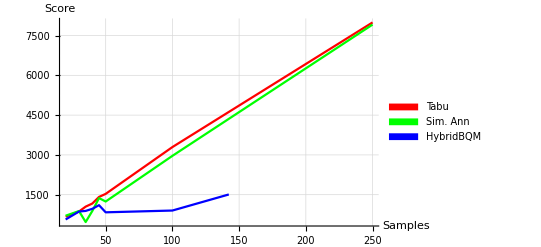

```mathematica
Legended[
Show[adapTabuInerPlot,adapSimInerPlot,adapHybridInerPlot,
AxesLabel->{"Samples", "Score"},
PlotRange->All, 
GridLines->Automatic],
SwatchLegend[ {Red, Green, Blue}, 
{"Tabu", "Sim. Ann", "HybridBQM"} ]
]
```

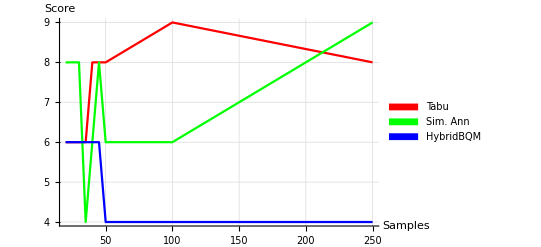

```mathematica
Legended[
Show[adapTabuIterPlot, adapSimIterPlot, adapHybridIterPlot,
AxesLabel->{"Samples", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[ {Red, Green, Blue}, 
{"Tabu", "Sim. Ann", "HybridBQM"} ]
]
```

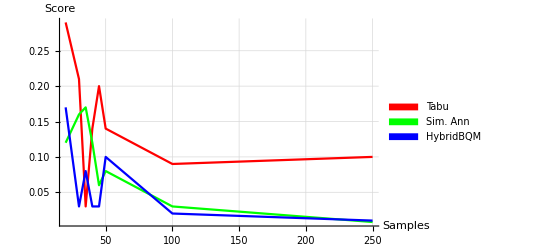

```mathematica
Legended[
Show[adapTabuHomPlot, adapSimHomPlot, adapHybridHomPlot,
AxesLabel->{"Samples", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[ {Red, Green, Blue}, 
{"Tabu", "Sim. Ann", "HybridBQM"} ]
]
```

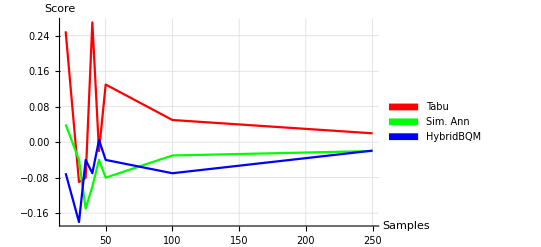

```mathematica
Legended[
Show[adapTabuSilPlot, adapSimSilPlot, adapHybridSilPlot,
AxesLabel->{"Samples", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[ {Red, Green, Blue}, 
{"Tabu", "Sim. Ann", "HybridBQM"} ]
]
```

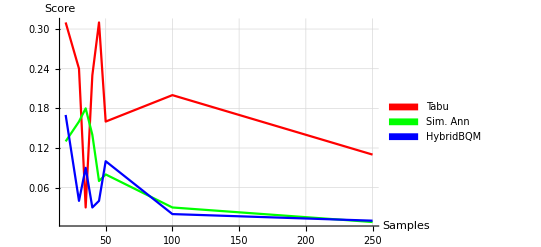

```mathematica
Legended[
Show[adapTabuComPlot, adapSimComPlot, adapHybridComPlot,
AxesLabel->{"Samples", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[ {Red, Green, Blue}, 
{"Tabu", "Sim. Ann", "HybridBQM"} ]
]
```

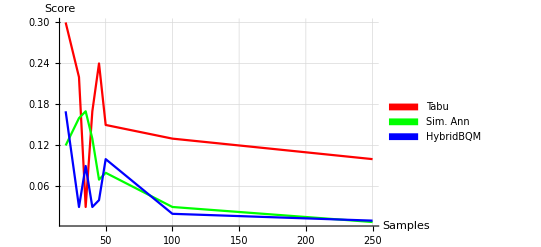

```mathematica
Legended[
Show[adapTabuVmPlot, adapSimVmPlot, adapHybridVmPlot,
AxesLabel->{"Samples", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[ {Red, Green, Blue}, 
{"Tabu", "Sim. Ann", "HybridBQM"} ]
]
```

```mathematica
adapKmDefIter={{20,5},{30,5},{35,3},{40,7},{45,3},{50,5},{100,22},{250,22}};

adapKmDefIner={{20,25.67},{30,32.49},{35,39.23},{40,40.14},{45,54.07},{50,59.06},{100,128.89},{250,326.94}};

adapKmDefSil={{20,0.34},{30,0.32},{35,0.36},{40,0.41},{45,0.37},{50,0.39},{100,0.34},{250,0.38}};

adapKmDefHom={{20,0.49},{30,0.26},{35,0.25},{40,0.36},{45,0.46},{50,0.42},{100,0.23},{250,0.31}};

adapKmDefCom={{20,0.50},{30,0.27},{35,0.29},{40,0.37},{45,0.46},{50,0.43},{100,0.23},{250,0.31}};

adapKmDefVm={{20,0.49},{30,0.26},{35,0.27},{40,0.36},{45,0.46},{50,0.43},{100,0.23},{250,0.31}};
```

```mathematica
adapKmTabuIter={{20,6},{30,6},{35,4},{40,7},{45,9},{50,8},{100,11},{250,16}};

adapKmTabuIner={{20,26.83},{30,38.31},{35,58.46},{40,61.15},{45,54.23},{50,59.35},{100,132.92},{250,327.47}};

adapKmTabuSil={{20,0.35},{30,0.28},{35,0.32},{40,0.29},{45,0.39},{50,0.38},{100,0.31},{250,0.38}};

adapKmTabuHom={{20,0.36},{30,0.23},{35,0.15},{40,0.19},{45,0.41},{50,0.38},{100,0.31},{250,0.38}};

adapKmTabuCom={{20,0.38},{30,0.27},{35,0.29},{40,0.26},{45,0.41},{50,0.39},{100,0.18},{250,0.30}};

adapKmTabuVm={{20,0.37},{30,0.25},{35,0.20},{40,0.22},{45,0.41},{50,0.39},{100,0.18},{250,0.30}};
```

```mathematica
adapKmSimIter={{20,6},{30,9},{35,5},{40,7},{45,9},{50,8},{100,14},{250,10}};

adapKmSimIner={{20,26.83},{30,34.11},{35,39.23},{40,61.15},{45,54.23},{50,59.35},{100,128.89},{250,327.47}};

adapKmSimSil={{20,0.35},{30,0.30},{35,0.36},{40,0.29},{45,0.39},{50,0.38},{100,0.34},{250,0.38}};

adapKmSimHom={{20,0.36},{30,0.29},{35,0.25},{40,0.19},{45,0.41},{50,0.38},{100,0.23},{250,0.29}};

adapKmSimCom={{20,0.38},{30,0.29},{35,0.29},{40,0.26},{45,0.41},{50,0.39},{100,0.23},{250,0.30}};

adapKmSimVm={{20,0.37},{30,0.29},{35,0.27},{40,0.22},{45,0.41},{50,0.39},{100,0.23},{250,0.30}};


adapKmHybridIter={{20,6},{30,6},{35,6},{40,7},{45,9},{50,6},{100,8},{250,13}};

adapKmHybridIner={{20,26.83},{30,38.31},{35,53.87},{40,61.15},{45,54.23},{50,59.35},{100,129.54},{250,326.94}};

adapKmHybridSil={{20,0.35},{30,0.28},{35,0.34},{40,0.29},{45,0.39},{50,0.38},{100,0.34},{250,0.38}};

adapKmHybridHom={{20,0.36},{30,0.23},{35,0.17},{40,0.19},{45,0.41},{50,0.38},{100,0.24},{250,0.31}};

adapKmHybridCom={{20,0.38},{30,0.27},{35,0.30},{40,0.26},{45,0.41},{50,0.39},{100,0.25},{250,0.31}};

adapKmHybridVm={{20,0.37},{30,0.25},{35,0.22},{40,0.22},{45,0.41},{50,0.39},{100,0.25},{250,0.31}};
```

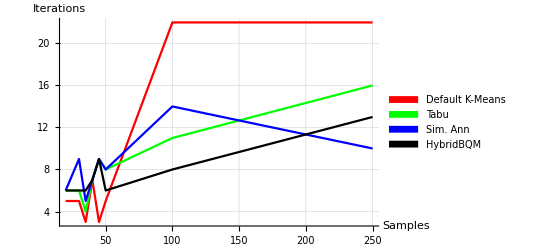

```mathematica
adapDefKmIterPlot = ListLinePlot[adapKmDefIter,PlotStyle->{Red}];
adapDefKmInerPlot = ListLinePlot[adapKmDefIner,PlotStyle->{Red}];
adapDefKmSilPlot = ListLinePlot[adapKmDefSil,PlotStyle->{Red}];
adapDefKmHomPlot = ListLinePlot[adapKmDefHom,PlotStyle->{Red}];
adapDefKmComPlot = ListLinePlot[adapKmDefCom,PlotStyle->{Red}];
adapDefKmVmPlot = ListLinePlot[adapKmDefVm,PlotStyle->{Red}];

adapTabuKmIterPlot=ListLinePlot[adapKmTabuIter,PlotStyle->{Green}];
adapTabuKmInerPlot=ListLinePlot[adapKmTabuIner,PlotStyle->{Green}];
adapTabuKmSilPlot=ListLinePlot[adapKmTabuSil,PlotStyle->{Green}];
adapTabuKmHomPlot=ListLinePlot[adapKmTabuHom,PlotStyle->{Green}];
adapTabuKmComPlot=ListLinePlot[adapKmTabuCom,PlotStyle->{Green}];
adapTabuKmVmPlot=ListLinePlot[adapKmTabuVm,PlotStyle->{Green}];

adapSimKmIterPlot=ListLinePlot[adapKmSimIter,PlotStyle->{Blue}];
adapSimKmInerPlot=ListLinePlot[adapKmSimIner,PlotStyle->{Blue}];
adapSimKmSilPlot=ListLinePlot[adapKmSimSil,PlotStyle->{Blue}];
adapSimKmHomPlot=ListLinePlot[adapKmSimHom,PlotStyle->{Blue}];
adapSimKmComPlot=ListLinePlot[adapKmSimCom,PlotStyle->{Blue}];
adapSimKmVmPlot=ListLinePlot[adapKmSimVm,PlotStyle->{Blue}];

adapHybridKmIterPlot=ListLinePlot[adapKmHybridIter,PlotStyle->{Black}];
adapHybridKmInerPlot=ListLinePlot[adapKmHybridIner,PlotStyle->{Black}];
adapHybridKmSilPlot=ListLinePlot[adapKmHybridSil,PlotStyle->{Black}];
adapHybridKmHomPlot=ListLinePlot[adapKmHybridHom,PlotStyle->{Black}];
adapHybridKmComPlot=ListLinePlot[adapKmHybridCom,PlotStyle->{Black}];
adapHybridKmVmPlot=ListLinePlot[adapKmHybridVm,PlotStyle->{Black}];



Legended[Show[adapDefKmIterPlot,adapTabuKmIterPlot,adapSimKmIterPlot,adapHybridKmIterPlot,AxesLabel->{"Samples","Iterations"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu","Sim. Ann","HybridBQM"}]]
```

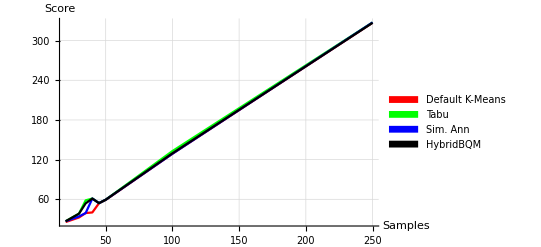

ListLinePlot::lpn: adapDefIner is not a list of numbers or pairs of numbers.

```mathematica
Legended[Show[adapDefKmInerPlot,adapTabuKmInerPlot,adapSimKmInerPlot,adapHybridKmInerPlot,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu","Sim. Ann","HybridBQM"}]]
```

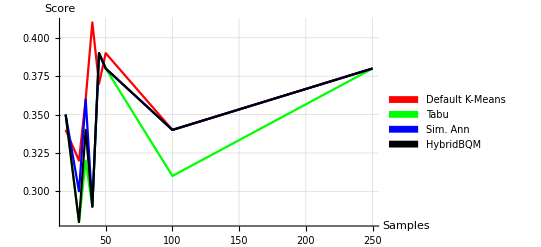

```mathematica
Legended[Show[adapDefKmSilPlot,adapTabuKmSilPlot,adapSimKmSilPlot,adapHybridKmSilPlot,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu","Sim. Ann","HybridBQM"}]]
```

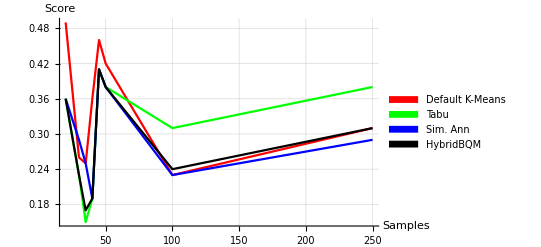

```mathematica
Legended[Show[adapDefKmHomPlot,adapTabuKmHomPlot,adapSimKmHomPlot,adapHybridKmHomPlot,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu","Sim. Ann","HybridBQM"}]]
```

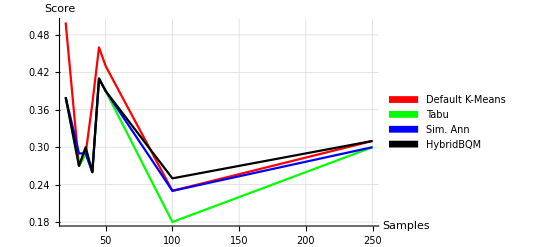

```mathematica
Legended[Show[adapDefKmComPlot,adapTabuKmComPlot,adapSimKmComPlot,adapHybridKmComPlot,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu","Sim. Ann","HybridBQM"}]]
```

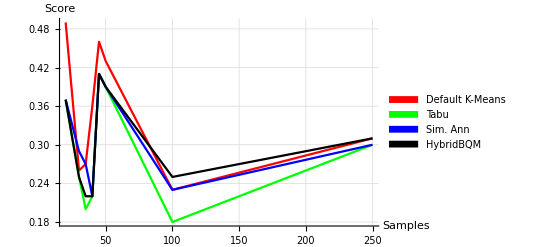

```mathematica
Legended[Show[adapDefKmVmPlot,adapTabuKmVmPlot,adapSimKmVmPlot,adapHybridKmVmPlot,AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu","Sim. Ann","HybridBQM"}]]
```